```mathematica
Text["Jatin's Equations for Problem 1:"]
```

Jatin's Equations for Problem 1:

```mathematica
p11Y1[x_]= Sqrt[-12*(x-3)]
p11Y2[x_]= -1 * Sqrt[-12*(x-3)]

p12X[t_] = t
p12Y[t_] = (t*t/12) -3

p13R[x_] = 6/(1-Cos[x])
p13Y1[x_] = Sqrt[(x+3)*12]
p13Y2[x_] = -1*Sqrt[(x+3)*12]
```

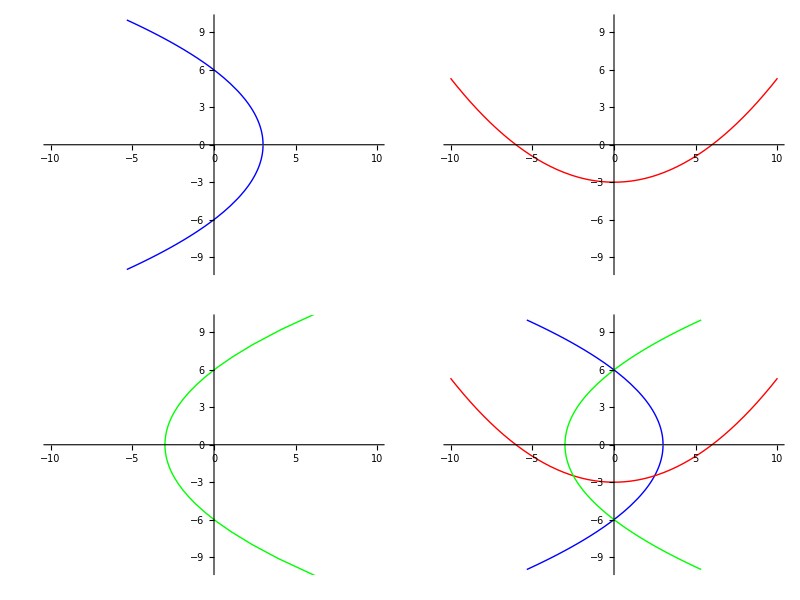

```mathematica
Grid[
{
{
Plot[
{p11Y1[x],p11Y2[x]},{x,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->{{Blue,Thick},{Blue,Thick}}
],
ParametricPlot[
{p12X[t],p12Y[t]},{t,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->{Red,Thick}
]
},
{
PolarPlot[p13R[x],{x,0.001,2Pi-0.001},PlotRange->{{-10,10},{-10,10}},PlotStyle->{Green,Thick}],
Plot[{p11Y1[x],p11Y2[x],p12Y[x],p13Y1[x],p13Y2[x]},{x,-10,10},PlotRange -> {{-10,10},{-10,10}},PlotStyle->{{Blue,Thick},{Blue,Thick},{Red,Thick},{Green,Thick},{Green,Thick}}]
}
},Frame->All
]
```

```mathematica
Text["Jatin's Equations for Problem 2:"]
```

Jatin's Equations for Problem 2:

```mathematica
p21Y1[x_] = Sqrt[(25 - (x-3)^2)*16/25]
p21Y2[x_] = -1*Sqrt[(25 - (x-3)^2)*16/25]

p22X [t_] = 5*Cos[t]-3
p22Y[t_]= 4*Sin[t]
p22Y1[x_] = Sqrt[(25 - (x+3)^2)*16/25]
p22Y2[x_] = -1*Sqrt[(25 - (x+3)^2)*16/25]

p23R[x_] = 16/(5-3*Sin[x])
p23Y1[x_] = Sqrt[(16 - x^2)*25/16]+3
p23Y2[x_] =-1*Sqrt[(16 - x^2)*25/16]+3
```

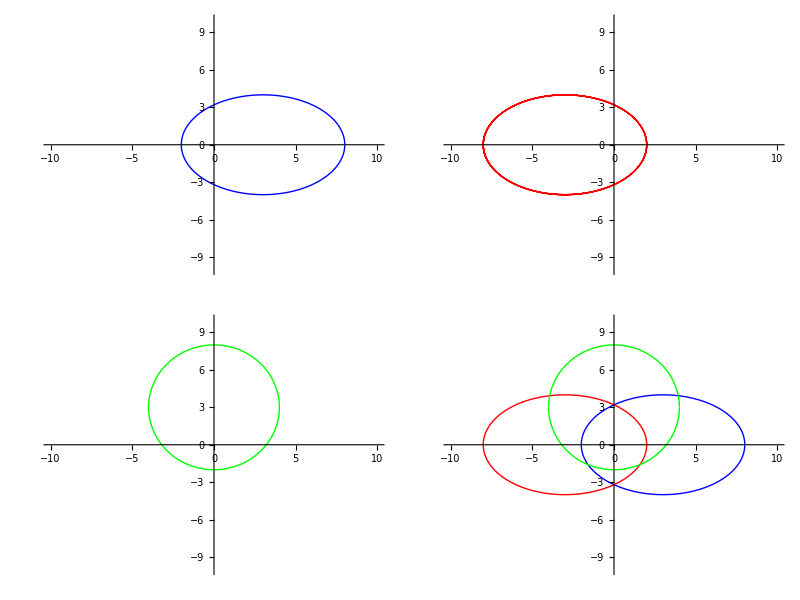

```mathematica
Grid[
{
{
Plot[
{p21Y1[x],p21Y2[x]},{x,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->{{Blue,Thick},{Blue,Thick}}
],
ParametricPlot[
{p22X[t],p22Y[t]},{t,-10,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->{Red,Thick}
]
},
{
PolarPlot[p23R[x],{x,0.001,2Pi-0.001},PlotRange->{{-10,10},{-10,10}},PlotStyle->{Green,Thick}],
Plot[{p21Y1[x],p21Y2[x],p22Y1[x],p22Y2[x],p23Y1[x],p23Y2[x]},{x,-10,10},PlotRange -> {{-10,10},{-10,10}},PlotStyle->{{Blue,Thick},{Blue,Thick},{Red,Thick},{Red,Thick},{Green,Thick},{Green,Thick}}]
}
},Frame->All
]
```